```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
options={BaseStyle->{FontSize->Medium},Frame->{True,True,False,False},FrameLabel->{"θ","p(θ)"},FrameTicks->{None,None}};
```

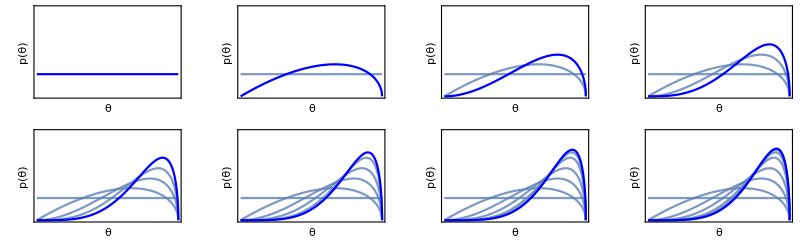

```mathematica
g1=Plot[{PDF[BetaDistribution[1,1],x]},{x,0,1},PlotRange->{Automatic,{0,4}},PlotStyle->Blue,Evaluate@options];
g2=Plot[{PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[2,1.5],x]},{x,0,1},PlotRange->{Automatic,{0,4}},PlotStyle->{{Opacity[0.8],ColorData[97,"ColorList"][[1]]},Blue},Evaluate@options];
g3=Plot[{PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[2,1.5],x],PDF[BetaDistribution[3,1.5],x]},{x,0,1},PlotRange->{Automatic,{0,4}},PlotStyle->{{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},Blue},Evaluate@options];
g4=Plot[{PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[2,1.5],x],PDF[BetaDistribution[3,1.5],x],PDF[BetaDistribution[4,1.5],x]},{x,0,1},PlotRange->{Automatic,{0,4}},PlotStyle->{{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},Blue},Evaluate@options];
g5=Plot[{PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[2,1.5],x],PDF[BetaDistribution[3,1.5],x],PDF[BetaDistribution[4,1.5],x],PDF[BetaDistribution[5,1.5],x]},{x,0,1},PlotRange->{Automatic,{0,4}},PlotStyle->{{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},Blue},Evaluate@options];
g6=Plot[{PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[2,1.5],x],PDF[BetaDistribution[3,1.5],x],PDF[BetaDistribution[4,1.5],x],PDF[BetaDistribution[5,1.5],x],PDF[BetaDistribution[5.5,1.5],x]},{x,0,1},PlotRange->{Automatic,{0,4}},PlotStyle->{{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},Blue},Evaluate@options];
g7=Plot[{PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[2,1.5],x],PDF[BetaDistribution[3,1.5],x],PDF[BetaDistribution[4,1.5],x],PDF[BetaDistribution[5,1.5],x],PDF[BetaDistribution[5.5,1.5],x],PDF[BetaDistribution[5.75,1.5],x]},{x,0,1},PlotRange->{Automatic,{0,4}},PlotStyle->{{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},Blue},Evaluate@options];
g8=Plot[{PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[2,1.5],x],PDF[BetaDistribution[3,1.5],x],PDF[BetaDistribution[4,1.5],x],PDF[BetaDistribution[5,1.5],x],PDF[BetaDistribution[5.5,1.5],x],PDF[BetaDistribution[5.75,1.5],x],PDF[BetaDistribution[5.85,1.5],x]},{x,0,1},PlotRange->{Automatic,{0,4}},PlotStyle->{{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},{Opacity[0.8],ColorData[97,"ColorList"][[1]]},Blue},Evaluate@options];
gFinal=Show[GraphicsGrid[{{g1,g2,g3,g4},{g5,g6,g7,g8}}],ImageSize->800]
```

```mathematica
Export["metropolisHastings_convergenceToPosterior.pdf",gFinal]
```

metropolisHastings_convergenceToPosterior.pdf